PROJEKTNA NALOGA PRI PREDMETU ROM: Hitrostno plezanje

Na treningu športnega plezanja sem sestavila dve smeri in štopala vadeče, kako hitro ju bodo preplezali. Vsak je vsako smer preplezal štirikrat. Rezultate sem vnesla v exel razpredilnico in jo vnesla v Mathematico.

```mathematica
Directory[]
```

C:\Users\Špela\Documents

```mathematica
NotebookDirectory[]
```

E:\SPELA\PRAKTICNA MAT\ROM\Projektna naloga\

```mathematica
SetDirectory[NotebookDirectory[]]
```

E:\SPELA\PRAKTICNA MAT\ROM\Projektna naloga

Najprej sem ustrezno nastavila direktorij.

```mathematica
Directory[]
```

E:\SPELA\PRAKTICNA MAT\ROM\Projektna naloga

```mathematica
podatki = Import["hitrost.xlsx"] // First
```

{{Ime,Priimek,1.smer prvič ,1.smer drugič,1.smer tretjič,1.smer četrtič,2.smer prvič,2.smer drugič ,2.smer tretjič,2.smer četrtič},{Maks,Bevk,16.,24.,15.2,12.,17.6,15.9,14.8,9.6},{Maks,Bajda,24.3,18.7,18.2,13.5,15.8,19.,22.1,14.},{Ožbej,Stanek,34.,28.8,32.,13.1,19.1,21.2,41.,30.6},{Maj,Bergant,10.,10.5,9.,11.6,10.6,8.2,12.2,9.2},{Jaka ,Žumer,19.,40.,29.7,16.8,20.,20.6,29.2,15.7},{Žiga,Čarman,15.6,18.3,23.4,23.4,18.6,16.53,30.,33.5},{Juš,Lampe,17.4,21.3,16.,21.3,18.6,16.3,20.,20.},{Dorjan ,Fritz,19.,20.,28.5,27.7,13.,12.,26.5,17.2}}

```mathematica
TableForm[podatki]
```

Ime | Priimek | 1.smer prvič  | 1.smer drugič | 1.smer tretjič | 1.smer četrtič | 2.smer prvič | 2.smer drugič  | 2.smer tretjič | 2.smer četrtič
Maks | Bevk | 16. | 24. | 15.2 | 12. | 17.6 | 15.9 | 14.8 | 9.6
Maks | Bajda | 24.3 | 18.7 | 18.2 | 13.5 | 15.8 | 19. | 22.1 | 14.
Ožbej | Stanek | 34. | 28.8 | 32. | 13.1 | 19.1 | 21.2 | 41. | 30.6
Maj | Bergant | 10. | 10.5 | 9. | 11.6 | 10.6 | 8.2 | 12.2 | 9.2
Jaka  | Žumer | 19. | 40. | 29.7 | 16.8 | 20. | 20.6 | 29.2 | 15.7
Žiga | Čarman | 15.6 | 18.3 | 23.4 | 23.4 | 18.6 | 16.53 | 30. | 33.5
Juš | Lampe | 17.4 | 21.3 | 16. | 21.3 | 18.6 | 16.3 | 20. | 20.
Dorjan  | Fritz | 19. | 20. | 28.5 | 27.7 | 13. | 12. | 26.5 | 17.2

Oblikovala sem tabelo v Mathematici s pomočjo TableForm.

```mathematica
Export["test.pdf", podatki // TableForm]
```

test.pdf

Izvozila sem tudi urejeno testno tabelo.

```mathematica
Imena[podatki_] := podatki[[1]]
Imena[podatki]
```

{Ime,Priimek,1.smer prvič ,1.smer drugič,1.smer tretjič,1.smer četrtič,2.smer prvič,2.smer drugič ,2.smer tretjič,2.smer četrtič}

S tem ukazom sem dobila prvo vrstico oz. vrstico, ki nam pove kaj je kje zapisano.

```mathematica
Podatki[podatki_] := Rest[podatki]
Podatki[podatki]
```

{{Maks,Bevk,16.,24.,15.2,12.,17.6,15.9,14.8,9.6},{Maks,Bajda,24.3,18.7,18.2,13.5,15.8,19.,22.1,14.},{Ožbej,Stanek,34.,28.8,32.,13.1,19.1,21.2,41.,30.6},{Maj,Bergant,10.,10.5,9.,11.6,10.6,8.2,12.2,9.2},{Jaka ,Žumer,19.,40.,29.7,16.8,20.,20.6,29.2,15.7},{Žiga,Čarman,15.6,18.3,23.4,23.4,18.6,16.53,30.,33.5},{Juš,Lampe,17.4,21.3,16.,21.3,18.6,16.3,20.,20.},{Dorjan ,Fritz,19.,20.,28.5,27.7,13.,12.,26.5,17.2}}

Podatki vrnejo preostal del tabele, se pravi vnešene podatke otrok in njihove hitrosti.

```mathematica
IndeksStolpca[podatki_, stolpec_] :=  If[Position[Imena[podatki], stolpec] == {}, Null,  Position[Imena[podatki], stolpec]//First // First]
```

```mathematica
IndeksStolpca[podatki, "Ime"]
```

1

Izvemo, v katerem stolpcu se nahajajo določeni podatki.

```mathematica
IndeksStolpca[podatki, "2.smer prvič"]
```

7

```mathematica
Stolpec[podatki_, stolpec_] :=Transpose[Rest[podatki]][[IndeksStolpca[podatki, stolpec]]]
```

```mathematica
Stolpec[podatki, "Ime"]
```

{Maks,Maks,Ožbej,Maj,Jaka ,Žiga,Juš,Dorjan }

Vrne določeni stolpec. (V tem primeru stolpec z imeni.)

```mathematica
Stolpec[podatki,"2.smer prvič"]
```

{17.6,15.8,19.1,10.6,20.,18.6,18.6,13.}

Vrne stolpec s časi preplezane druge smeri v prvem poskusu.

```mathematica
podatki[[2]]
```

```mathematica
{"Maks","Bevk",16.,24.,15.2,12.,17.6,15.9,14.8,9.6}
```

Dobimo celotno vrstico s podatki za določenega vadečega, v tem primeru za Bevk Maksa.

```mathematica
Casi[otrok_] := Delete[Delete[podatki[[otrok]],1],1];
Casi[2]
```

{16.,24.,15.2,12.,17.6,15.9,14.8,9.6}

Funkcija Casi vrne čase posameznega otroka za vseh 8 smeri. Npr Casi[2] vrne vse čase od Maksa Bevka.

```mathematica
cas_Maks1 =  Delete[Delete[podatki[[2]],1],1]
```

{16.,24.,15.2,12.,17.6,15.9,14.8,9.6}

```mathematica
cas_Maks2 = Delete[Delete[podatki[[3]],1],1]
```

{24.3,18.7,18.2,13.5,15.8,19.,22.1,14.}

```mathematica
cas_Ozbej = Delete[Delete[podatki[[4]],1],1]
```

{34.,28.8,32.,13.1,19.1,21.2,41.,30.6}

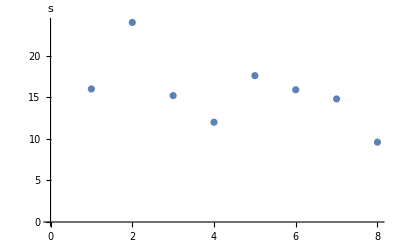

```mathematica
ListPlot[Quantity[{16.,24.,15.2,12.,17.6,15.9,14.8,9.6}, "Seconds"], AxesLabel -> Automatic]
```

Dobili smo graf s hitrostmi Maksovih (Bevk) preplezanih smeri.

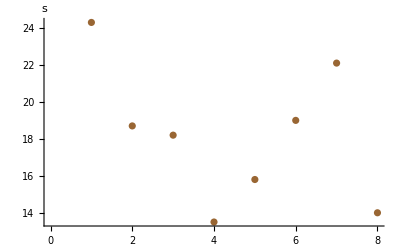

```mathematica
ListPlot[Quantity[Delete[Delete[podatki[[3]],1],1], "Seconds"], AxesLabel -> Automatic, PlotStyle -> Brown]
```

Dobili smo graf s hitrostmi Maksovih (Bajda) preplezanih smeri.

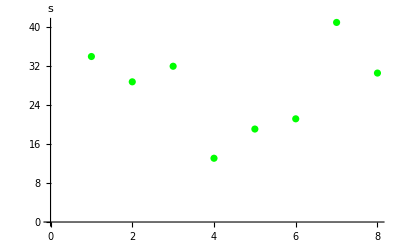

```mathematica
ListPlot[Quantity[Delete[Delete[podatki[[4]],1],1], "Seconds"], AxesLabel -> Automatic, PlotStyle -> Green]
```

Dobili smo graf s hitrostmi Ožbejevih preplezanih smeri.

Enako bi lahko naredili še za ostale. Iz grafa je razvidno (prve 4. oznake), kakšni so bili časi pri plezanju prve smeri in (od 5-8.oznake) časi pri plezanju druge smeri.
Iz grafa lahko razberemo, V katerem poiskusu jim je šlo najboljše in v katerem poiskusu so porabili največ časa. Iz tega lahko razberemo, kako na njih vpliva utrujenost ter poznavanje terena.

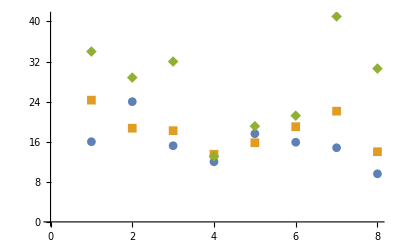

```mathematica
ListPlot[{{16.,24.,15.2,12.,17.6,15.9,14.8,9.6} , {24.3,18.7,18.2,13.5,15.8,19.,22.1,14.}, {34.,28.8,32.,13.1,19.1,21.2,41.,30.6}}, PlotMarkers -> Automatic]
```

Tukaj so prikazani časi preplezanih smeri za Maksa Bevka, Maksa Bajdo in Ožbeja.
Vidimo lahko, da so se pri prvi smeri vsi najbolj potrudili v četrtem - zadnjem poiskusu. Medtem ko so bili pri drugi smeri nekateri že utrujeni, in so posledični dosegli boljši čas v prvem poiskusu druge smeri.
Iz grafa je tudi razvidno, da je imel najboljše čase Maks Bevk, ki trenira najdlje izmed cele skupine.
Prav tako je razvidno, da hitrost dela največ problemov Ožbeju, ki je začel trenirat šele s tem šolskim letom.

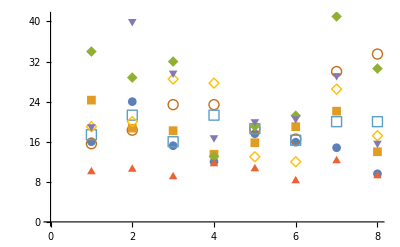

```mathematica
ListPlot[{Casi[2],Casi[3], Casi[4], Casi[5], Casi[6], Casi[7], Casi[8], Casi[9] }, PlotMarkers -> Automatic]
```

Na zgornji graf sem vnesla čase vseh smeri za vse tekmovalce.

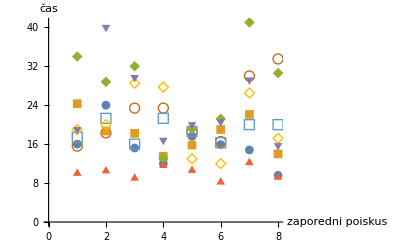

```mathematica
Show[%105,AxesLabel->{HoldForm[zaporedni poiskus],HoldForm[čas]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

```mathematica
Show[%106,ImageSize->Large]
```

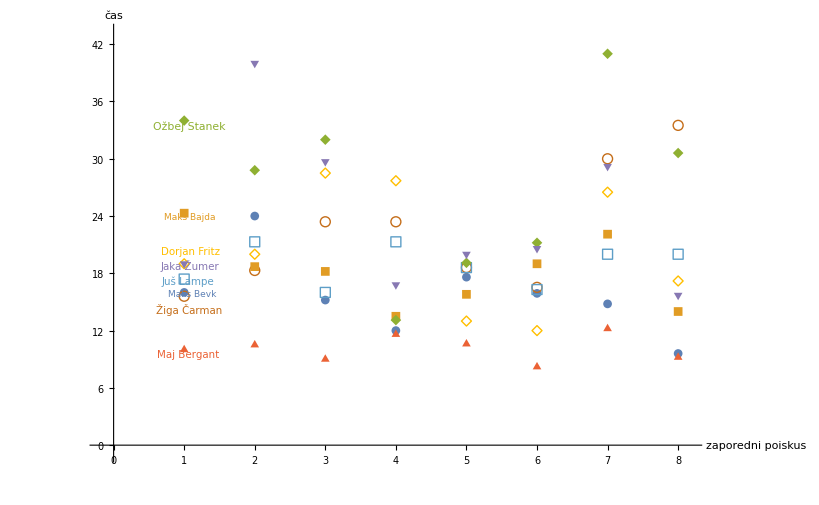

Na tem grafu so prikazani časi vseh tekmovalcev za posamičen poiskus plezanja smeri. Vidimo, da je imel najboljše čase otrok z oranžnimi trikotniki - Maj Bergant. 
Iz grafa lahko vidimo, v katerem poiskusu so se najbolj potrudili, pri prvi smeri je padel rekord v drugem poiskusu - Maj, na splošno pa je bila najboljše preplezana v četrtem poiskusu.
Med tem ko je pri drugi smeri prav tako Maj podrel rekord v drugem poiskusu, smer pa je bila v povprečju najboljše preplezana v prvem poiskusu. Tukaj je velik faktor tudi utrujenost, saj smo smeri plezali na koncu treninga, in se pri drugi smeri že močno pozna vpad energije.

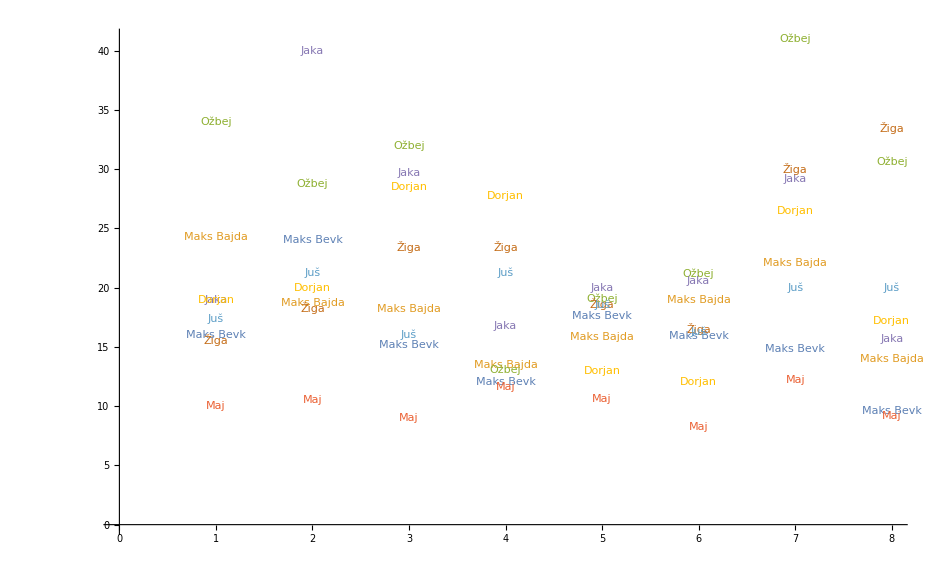

```mathematica
ListPlot[{Casi[2],Casi[3], Casi[4], Casi[5], Casi[6], Casi[7], Casi[8], Casi[9] }, PlotMarkers -> {"Maks Bevk","Maks Bajda","Ožbej","Maj","Jaka ","Žiga","Juš","Dorjan" }]
```

Naslednje meritve smo imeli 11.01.2019. Tokrat smo prav tako plezali dve smeri, ampak vsako samo trikrat. Podatke sem vnesla v excel preglednico hitrosti2, in jih uvozila v Mathematico.

```mathematica
podatki2 = Import["hitrost2.xlsx"] // First
```

{{Ime,Priimek,1.smer prvič ,1.smer drugič,1.smer tretjič,2.smer prvič ,2.smer drugič,2.smer tretjič},{Maks,Bevk,17.,12.3,3.7,21.8,14.,7.6},{Ožbej,Stanek,20.,16.3,4.5,32.,13.7,8.},{Maj,Bergant,19.5,10.,3.8,20.4,6.9,8.1},{Jaka ,Žumer,14.,10.3,6.3,15.5,1.8,7.1},{Žiga,Čarman,30.,19.3,6.3,22.,13.2,7.8},{Juš,Lampe,11.9,11.3,7.8,12.4,15.4,14.3},{Dorjan ,Fritz,28.5,27.7,8.6,26.5,17.2,8.}}

```mathematica
TableForm[podatki2]
```

Ime | Priimek | 1.smer prvič  | 1.smer drugič | 1.smer tretjič | 2.smer prvič  | 2.smer drugič | 2.smer tretjič
Maks | Bevk | 17. | 12.3 | 3.7 | 21.8 | 14. | 7.6
Ožbej | Stanek | 20. | 16.3 | 4.5 | 32. | 13.7 | 8.
Maj | Bergant | 19.5 | 10. | 3.8 | 20.4 | 6.9 | 8.1
Jaka  | Žumer | 14. | 10.3 | 6.3 | 15.5 | 1.8 | 7.1
Žiga | Čarman | 30. | 19.3 | 6.3 | 22. | 13.2 | 7.8
Juš | Lampe | 11.9 | 11.3 | 7.8 | 12.4 | 15.4 | 14.3
Dorjan  | Fritz | 28.5 | 27.7 | 8.6 | 26.5 | 17.2 | 8.

```mathematica
Imena[podatki2_] := podatki2[[1]]
Imena[podatki2]
```

{Ime,Priimek,1.smer prvič ,1.smer drugič,1.smer tretjič,2.smer prvič ,2.smer drugič,2.smer tretjič}

```mathematica
Podatki[podatki2_] := Rest[podatki2]
Podatki[podatki2]
```

{{Maks,Bevk,17.,12.3,3.7,21.8,14.,7.6},{Ožbej,Stanek,20.,16.3,4.5,32.,13.7,8.},{Maj,Bergant,19.5,10.,3.8,20.4,6.9,8.1},{Jaka ,Žumer,14.,10.3,6.3,15.5,1.8,7.1},{Žiga,Čarman,30.,19.3,6.3,22.,13.2,7.8},{Juš,Lampe,11.9,11.3,7.8,12.4,15.4,14.3},{Dorjan ,Fritz,28.5,27.7,8.6,26.5,17.2,8.}}

```mathematica
IndeksStolpca[podatki2_, stolpec2_] :=  If[Position[Imena[podatki2], stolpec2] == {}, Null,  Position[Imena[podatki2], stolpec2]//First // First]
```

```mathematica
Stolpec[podatki2_, stolpec2_] :=Transpose[Rest[podatki2]][[IndeksStolpca[podatki2, stolpec2]]]
```

```mathematica
Casi[otrok2_] := Delete[Delete[podatki2[[otrok2]],1],1];
Casi[2]
```

{17.,12.3,3.7,21.8,14.,7.6}

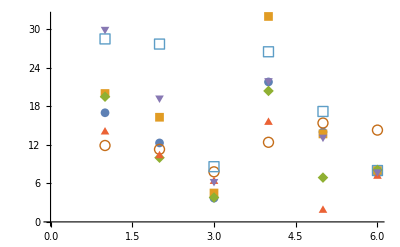

```mathematica
ListPlot[{Casi[2],Casi[3], Casi[4], Casi[5], Casi[6], Casi[7], Casi[8]}, PlotMarkers -> Automatic]
```

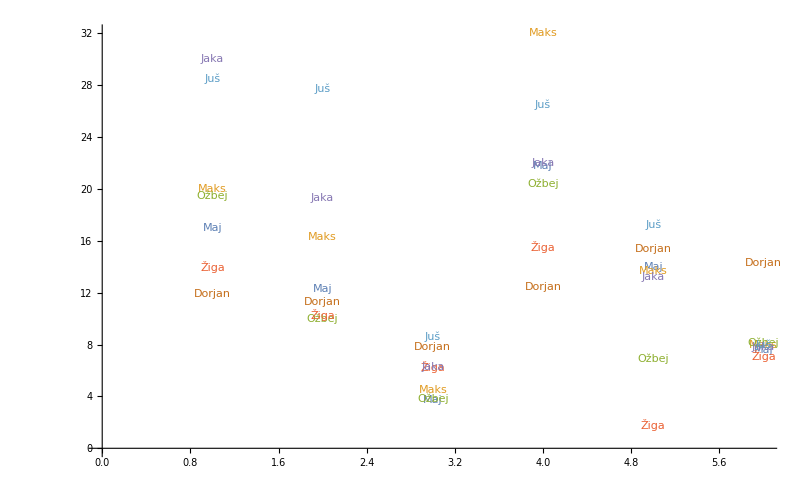

```mathematica
ListPlot[{Casi[2],Casi[3], Casi[4], Casi[5], Casi[6], Casi[7], Casi[8] }, PlotMarkers -> {"Maj","Maks","Ožbej","Žiga","Jaka ","Dorjan","Juš" }]
```

Če pogledamo tokratne rezultate, se je zelo očitno hitrost preplezane smeri skozi tri poiskuse pri večini izboljšala. Pri prvi smeri so daleč najboljši rezultati v tretjem poiskusu - celonajslabši je v tretjem poiskusu splezal bolje kot v prejšnjem poiskusu najboljši. Prav tako so se pri drugi smeri rezultati izboljšali v zadnjem poiskusu. Izstopa Žiga, ki je podrl rekord preplezane druge smeri v drugem poiskusu - po domače povedano je ‘fejkal’ smer in skočil iz enega dela na drugega, kar ni po pravilih. Rezultat pa so bili na splošnjo boljši kot pri prejšnjem, zgoraj opisanem treningu.

Seminarska naloga se mi je zdela uporabna iz vidika matematike - naučila sem se kar nekaj novih stvari, ki jih Mathematica zmore, spoznala sem par lastnosti pri oblikovanju grafov in pridobivanju podatkov iz tabel, poleg tega pa sem spoznala še novo metodo za primerjanje rezultatov svojih vadečih, ki jo bom sigurno še kdaj uporabila.

Špela Šter 																				Februar 2019